```mathematica
Clear["Global'*"]
d1=0.2;
d2=0.06;
mu=0.8;
cof=0.00125;(*квадрат растояние hw*)
T=0.0086;(*100 K*)
M1[m1_]=(d1-m1);
eta1[m1_]:=m1/d1;
nu=d2/d1;
{d1-d2, d1+d2, d2/d1}
```

{0.14,0.26,0.3}

```mathematica
energy[n_, B_, m1_, z_] = √(cof * n + (m1 - √(d2^2+d1^2-2*d1*d2*Cos[z]))^2);
{energy[0, 8, 0.15, Pi], energy[500, 8, 0.15, 0]}
```

{0.11,0.790633}

```mathematica
a1[B_,m1_]=(4*Pi*d1*d2*Abs[(1-eta1[m1])])/(cof*B) ;
b1[B_,m1_]=(2*Pi*(mu^2-(d1-m1)^2))/(cof*B);
c1[B_]=(2*Pi^2*T*mu)/(cof*B);
A11[m1_]=(1-eta1[m1])^2+(eta1[m1]^2*nu^2)/4;
B1[B_,m1_]=4/a1[B,m1]*((1-eta1[m1])^2+eta1[m1]^2*nu^2);
C1[B_,m1_]=(12*eta1[m1]^2*nu^2)/a1[B,m1]^2;
D1[B_,m1_]=(8*eta1[m1]*nu)/a1[B,m1];
tg[B_,m1_]=B1[B,m1]/(4*A11[m1]-C1[B,m1]);
phi[B_,m1_]=ArcTan[B1[B,m1]/(4*A11[m1]-C1[B,m1])];
```

```mathematica
sigma1[B_,m1_]:=1-(4 A11[m1]-C1[B,m1])/A11[m1]*Sqrt[2/(Pi*a1[B,m1])*(1+tg[B,m1]^2)]*Cos[(2*Pi)/(cof*B)*(mu^2-(d1-m1)^2)]*Cos[a1[B,m1]-Pi/4+ArcTan[tg[B,m1]]];
sigma2[B_,m1_]=-D1[B,m1]/A11[m1]*Sqrt[2/(Pi*a1[B,m1])*(1+tg[B,m1]^2)]*Sin[(2*Pi)/(cof*B)*(mu^2-(d1-m1)^2)]*Cos[a1[B,m1]-Pi/4];
sigma3[B_,m1_]=(4 A11[m1]-C1[B,m1])/A11[m1]*2/(Pi*a1[B,m1])*(1+Sqrt[1+tg[B,m1]^2]*Cos[2*a1[B,m1]-Pi/2+phi[B,m1]]);
Rt[B_, T1_] = (2*Pi^2*mu)/(cof*B)*T1/Sinh[(2*Pi^2*mu*T1)/(cof*B)];
Magt[B_,m1_,T1_]=BesselJ[0,a1[B,m1]]*Sin[b1[B,m1]]*Rt[B, T1];
sigmat[B_,m1_,T1_] = (sigma1[B, m1] + sigma2[B, m1])*Rt[B, T1] + sigma3[B,m1];
```

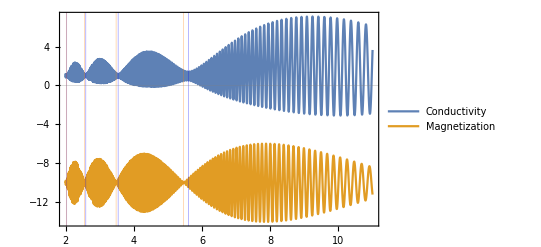

```mathematica
m2 = 0.25;
Plot[{sigmat[B,m2, T/1000],10* Magt[B,m2, T/1000] - 10},{B,2,11},Frame->True,PlotLegends->{"Conductivity","Magnetization"}, GridLines->{{{2.03, Blue},{2.02, Orange},{2.59,  Blue},{2.55,  Orange},  {3.54,  Blue}, {3.48,  Orange}, {5.60,  Blue}, {5.46,  Orange}}, {0}}]
```

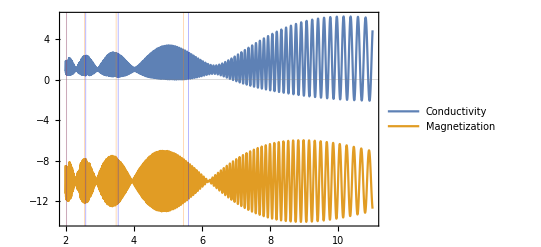

```mathematica
m2 = 0.25665;
Plot[{sigmat[B,m2, T/1000],10* Magt[B,m2, T/1000] - 10},{B,2,11},Frame->True,PlotLegends->{"Conductivity","Magnetization"}, GridLines->{{{2.03, Blue},{2.02, Orange},{2.59,  Blue},{2.55,  Orange},  {3.54,  Blue}, {3.48,  Orange}, {5.60,  Blue}, {5.46,  Orange}}, {0}}]
```

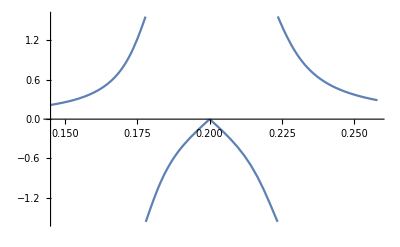

```mathematica
Plot[phi[5,m1], {m1, 0.145, 0.258}]
```

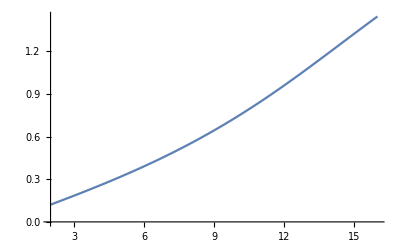

```mathematica
Plot[phi[B, 0.155], {B, 2, 16}]
```